## Computing intra-vs-inter edges for n = n_1*n_2

```mathematica
Binomial[Subscript[n, 1]*Subscript[n, 2],2]
```

1/2 n_1 n_2 (-1+n_1 n_2)

```mathematica
FullSimplify[Subscript[n, 1]*Binomial[Subscript[n, 2],2]+Binomial[Subscript[n, 1],2]*Subscript[n, 2]^2]
```

1/2 n_1 n_2 (-1+n_1 n_2)

```mathematica
x=(n2)/n;
x*n1*Binomial[n2,2]+(1-x)Binomial[n1,2]*n2^2/.n1->n/n2
```

1/2 (-1+n2) n2+1/2 n (-1+n/n2) n2 (1-n2/n)

```mathematica
Binomial[n2,2]
```

1/2 (-1+n2) n2

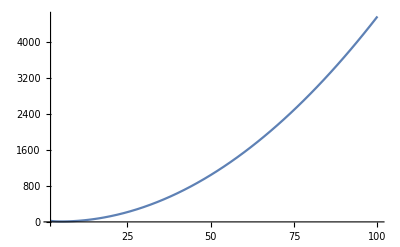

```mathematica
Plot[(n (1-5 (2+n-n^2/5+(-2+n/5) 5)))/(2 (-1+n)),{n,2,100}]
```

## A discussion on probability

```mathematica
FullSimplify[2/(Log[n]*(n/Log[n])^2)]
```

(2 Log[n])/n^2

```mathematica
Plot[{(2Log[n])/n,2 Log[n]/n^2,2/n},{n,3,50},PlotLabels->{"w/in tree edge probability","b/w tree edge probability","true uniform edge probability"},PlotStyle->AbsoluteThickness[4],AxesLabel->{"n","Probability of being selected"}]
```

-Graphics-

```mathematica
Plot[{2/(√n),2/(√n*(√n)^2),2/n},{n,3,50},PlotLabels->{"w/in tree edge probability","b/w tree edge probability","true uniform edge probability"},PlotStyle->AbsoluteThickness[4],AxesLabel->{"n","Probability of being selected"}]
```

-Graphics-

### Setting Them Equal

```mathematica
Reduce[n1*Binomial[n2,2]==Binomial[n1,2]*n2^2, {n1,n2},Integers]
```

(n1==1&&n2==1)||(n1==3&&n2==-1)||n1==0||n2==0

```mathematica
Min[Binomial[n1,2]*n2^2-n1*Binomial[n2,2], {n1,n2},Integers]
```

Min[ℤ,n1,n2,-1/2 n1 (-1+n2) n2+1/2 (-1+n1) n1 n2^2]

```mathematica
ContourPlot[Binomial[n1,2]*n2^2-n1*Binomial[n2,2],{n1,5,50},{n2,5,50},PlotLegends->Automatic]
```

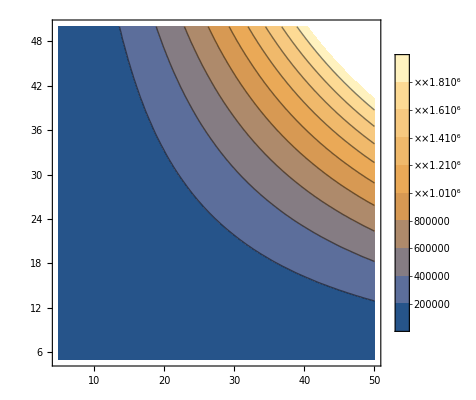
```mathematica
-Graphics-
Plot3D[Binomial[n1,2]*n2^2-n1*Binomial[n2,2],{n1,5,50},{n2,5,50},PlotLegends->Automatic]
```

```mathematica
Table[Binomial[n1,2]*(n/n1)^2-n1*Binomial[(n/n1),2],{n1, 1,10}]
```

{-4.5 n^2-0.5 n (-1+10. n)}

```mathematica
Plot[{Binomial[n1,2]*(n/n1)^2-n1*Binomial[(n/n1),2]
```

## Adding P(split) to my earlier numbers -- Idea was originally Dinesh’s

```mathematica
pwithin=2/n2;
pbetween=2/(n*n/n1);
x=(n2-1)/(n-1);(*This is the key part: the probability of being in the same group vs the different group needs to be added*)
pedge=FullSimplify[x*pwithin+(1-x)*pbetween]/.n->n1*n2
```

(2 (-n1 n2^2+n1^2 n2^2+n1^2 (-1+n2) n2^2))/(n1^2 n2^3 (-1+n1 n2))

Once groups are formed, yes, there is an unequal treatment of edges
...but, since all vertices are being treated fairly when being split up, we end up with equally-likely chances that P(v1, v2) for any v1,v2 in the ST
is the same.
Because ^ simplifies to 2/n
If this is true, this gives us a lot of flexibility with the parallel stuff, as it means the probability has been taken care of w.r.t 
partitioning the clique

```mathematica
%/.{n2->11,n->99, n1->9}
```

2/99

```mathematica
2/100
```

1/50

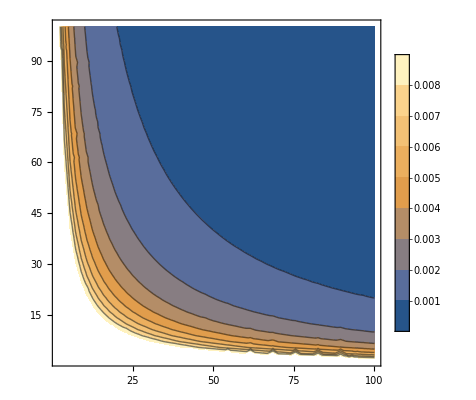

```mathematica
ContourPlot[{2/(n1*n2)},{n1,2,100},{n2,2,100},PlotLegends->Automatic]
```

```mathematica
ContourPlot[{(2 (-n1 n2^2+n1^2 n2^2+n1^2 (-1+n2) n2^2))/(n1^2 n2^3 (-1+n1 n2))},{n1,2,100},{n2,2,100},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot3D[2/(n1*n2)-(2 (-n1 n2^2+n1^2 n2^2+n1^2 (-1+n2) n2^2))/(n1^2 n2^3 (-1+n1 n2)),{n1,2,50},{n2,2,50}]
```

-Graphics3D-

```mathematica
FullSimplify[(2 (-n1 n2^2+n1^2 n2^2+n1^2 (-1+n2) n2^2))/(n1^2 n2^3 (-1+n1 n2))]
```

2/(n1 n2)

## Unequal Partitions

Based on the previous discussion, we’re fine on uniform-random when it comes to equal group sizes (for cliques), which means a parallel algorithm
on a symmetric multiprocessor setup could easily be made: 
(1) Randomly partition
(2) Wilson each partition in parallel
(3) Treat each partition as a “supernode”, Wilson the supernodes
(4) Based on the superedges (i.e. which supernodes should be connected to what), randomly pick one of the many edges between each supernode
(5) Return!
Our previous analysis means this algorithm should be good when it comes to uniform randomness.

But modern architecture are, at the very least, asymmetric CPUs. So it would be nice if we could still be good from a uniform-random perspective if we could split into unequal groups,
that way we could put the larger groups onto the faster processors, giving us a better parallel efficiency.

That’s the setup for this next step: can we unequally split partition?

```mathematica
k=5;
groups=Array[g,k]
```

{g[1],g[2],g[3],g[4],g[5]}

```mathematica
{g[1],g[2],g[3],g[4],g[5]}
(* Can make that ^ sums to n a global assumption. Will it help? IDK!*)
$Assumptions=Total[groups]==n;
```

{g[1],g[2],g[3],g[4],g[5]}

```mathematica
Coefficient[#,x,k-2]&[∏_(i=1)^k (x-groups[[i]])](* This is the total number of "b/w" edges for a given grouping by Vieta's formula *)
```

g[1] g[2]+g[1] g[3]+g[2] g[3]+g[1] g[4]+g[2] g[4]+g[3] g[4]+g[1] g[5]+g[2] g[5]+g[3] g[5]+g[4] g[5]

Quick check : verify that my craziness ^ is actually true.
    I.e., verify that totalBetween + totalWithin = (n choose 2)

```mathematica
(* quick check: summing everything becomes what I expect it to be *)
totalBetween=Coefficient[#,x,k-2]&[∏_(i=1)^k (x-groups[[i]])];
totalWithin=∑_(i=1)^k Binomial[groups[[i]],2]; (* total w/in = ∑ (group[i] choose 2) *)
```

```mathematica
FullSimplify[totalBetween +totalWithin]/.Total[groups]->n (* Total[groups] === g[1]+g[2]+...+g[k]. So I'm saying g[1]+g[2]+...+g[k] = n *)
```

1/2 (-1+n) n

### Throwing in numbers

```mathematica
n1 = 4;
n2=7;
n3=9;
k=3;
n=n1+n2+n3;
```

```mathematica
Case11=n1/n*((n1-1)/(n-1));
Case22=n2/n*((n2-1)/(n-1));
Case33=n3/n*((n3-1)/(n-1));
Case12=n1/n*(n2/(n-1));
Case13=n1/n*(n3/(n-1));
Case21=n2/n*(n1/(n-1));
Case23=n2/n*(n3/(n-1));
Case31=n3/n*(n1/(n-1));
Case32=n3/n*(n2/(n-1));
```

```mathematica
Case11+Case22+Case33+Case12+Case21+Case13+Case31+Case23+Case32
```

1

```mathematica
Case11*2/n1+Case22*2/n2+Case33*2/n3+2/k*(Case12*1/(n1*n2)+Case21*1/(n1*n2)+Case32*1/(n3*n2)+Case23*1/(n3*n2)+Case13*1/(n3*n1)+Case31*1/(n3*n1))
```

1/10

```mathematica
2/n
```

1/10

```mathematica
Case21==Case12
```

True

### Generalize ^ for when we don’t hard-code groups

```mathematica
k=50;
groups=Array[g,k];
Clear[n];
$Assumptions=Total[groups]==n;
result={};
For[i=1,i<=k,i++,
 x=groups[[i]];
For[j=1,j≤k,j++,
y=groups[[j]];
If[i==j,
(* x == y means we're in a CaseXX condition *)
AppendTo[result,x/n*((x-1)/(n-1))*2/x],
(* x ≠ y means we're in a CaseXY condition -- x is N1, y is N2 *)
AppendTo[result,x/n*(y/(n-1))*2/k*1/(x*y)]]]];
FullSimplify[Total[result]]/.Total[groups]->n
```

2/n

```mathematica
result
```